JSON Import

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
ImportJSONData[files_]:=Module[{},
Switch[Head[files],
String,
Import[files,"RawJSON"],
List,
Import[#,"RawJSON"]&/@files
]
];
OpenJSONData[]:=Module[{files},
files=OpenJSONDialog[];
ImportJSONData[files]
];
```

Visualize and process input JSON

### Plots simulation data structure. Single or list of simulations data

```mathematica
plotSimData[data_, color_:RGBColor[0.368417, 0.506779, 0.709798],legend_:"" ]:=
ListPlot[
Flatten[data["Trees"]["Branches"][[All,"coords"]],{1}],
Joined->True,
PlotRange->{{0,(*data["Model", "width"]*)2},{0,(*data["Model", "height"]*)5.5}}, 
AspectRatio->1, 
PlotStyle->color,
(*PlotLegends->{legend},*)
AxesLabel->{"X","Y"}];
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

Comparing rivers

```mathematica
compare1[datas_, range_]:=Module[{savedOpt=Options[ListPlot],image,lbl=Style["η = "<>ToString[Row[(range-1)/10.,", "]],Black, 16]},
SetOptions[ListPlot,
PlotRange->{{0,2},{0,10}},AspectRatio->2,ImageSize->500,
Joined->True,Frame->{{True,True},{True,False}},FrameLabel->{{None,None},{lbl,None}},FrameTicksStyle->Directive[Black,16],
PlotStyle->Flatten[Table[Table[Directive[ColorData[97,"ColorList"][[i]],Thickness[0.01]],datas[[range[[i]],6,1,All,2]]//Length],{i,1,range//Length}]]];
image=ListPlot[Flatten[Table[Flatten[datas[[i,6,1,All,2]],{1}],{i,range}],1]];
SetOptions[ListPlot,savedOpt];
image]
```

```mathematica
compareRow[datas_, range_]:=Module[{image},
image=GraphicsRow[
Table[compare1[datas,{i}],{i,range}],
ImageSize->1200];
image]
```

```mathematica
compare15[datas_]:=Module[{image},
image=GraphicsRow[
Table[compare1[datas,{3*i+1,3*i+2,3*i+3}],{i,0,4}],
ImageSize->1200];
image]
```

```mathematica
compare20[datas_]:=Module[{image},
image=GraphicsGrid[{
Table[compare1[datas,{i}],{i,1,10}],
Table[compare1[datas,{i}],{i,11,20}]
},
ImageSize->800,Spacings->25];
image]
```

Sandbox

## Cutting rivers

```mathematica
cutRivers[data_, fileName_]:=Module[{initialDistance,toDrop,dataExport},
initialDistance = EuclideanDistance[#1,#2]&@@data["Trees","Branches"][[All,2,1]];
toDrop=Count[MapThread[EuclideanDistance,data["Trees","Branches"][[All,2]]],u_/;u>3initialDistance];
dataExport=data;
dataExport[[6,1,All,2]]=Drop[#,-toDrop]&/@data["Trees","Branches"][[All,2]];
Export[NotebookDirectory[]<>fileName,dataExport];
dataExport]
```

```mathematica
datas=OpenJSONData[](*data drom initialLength1*)
```

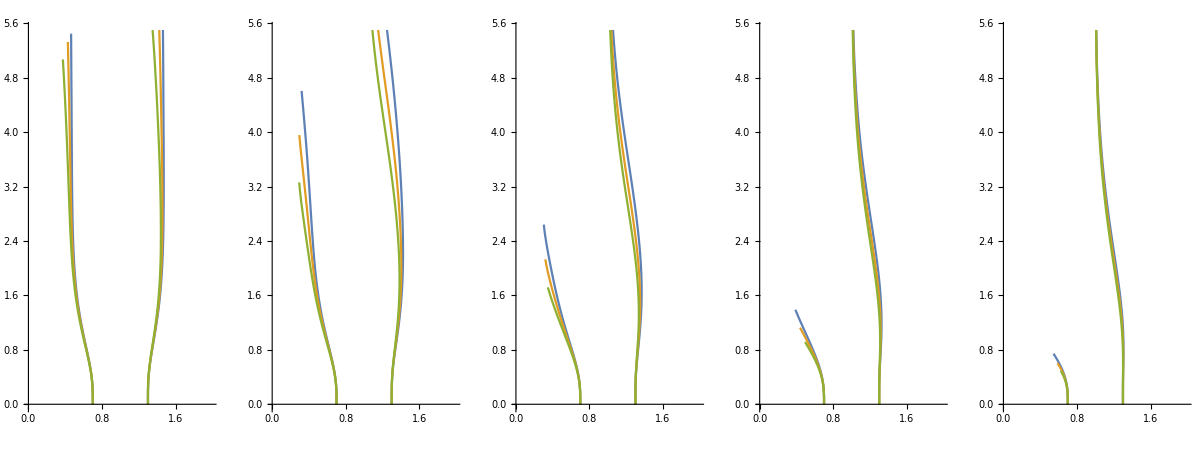

```mathematica
compare15[datas]
```

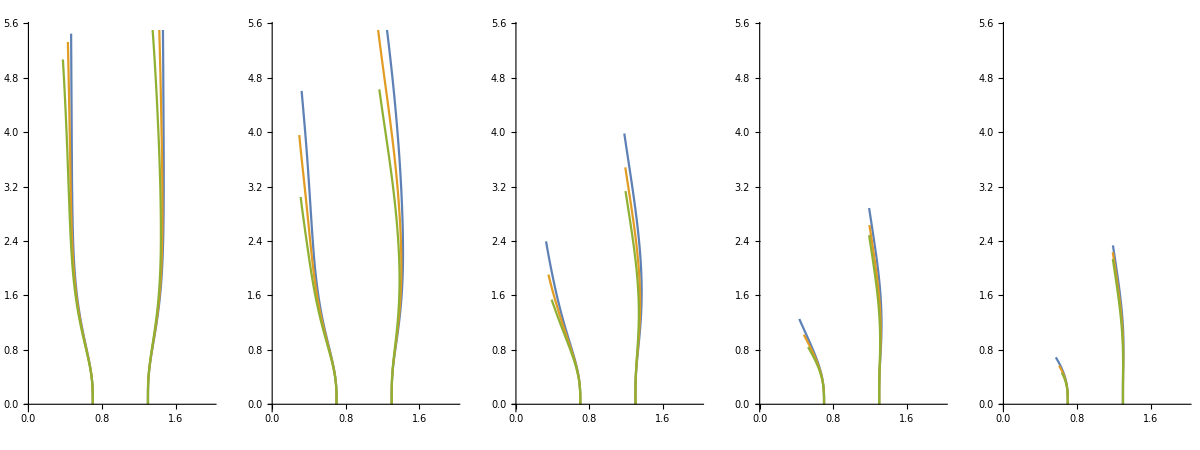

```mathematica
datasExport=MapThread[cutRivers,{datas,Table["initialLength1/cut_rivers/lap"<>ToString[index]<>".json",{index,Range@Length@datas}]}];compare15[datasExport]
```

## Comparing growth rate

```mathematica
compare1growth[datas_, range_,cut_]:=Module[{savedOpt=Options[ListPlot],image,lbl=Style["η = "<>ToString[Row[(range-1)/10.,", "]],Black, 16]},
SetOptions[ListPlot,
PlotRange->{{0,2},{0,10}},AspectRatio->1,ImageSize->500,
Joined->True,Frame->{{True,True},{True,False}},(*FrameLabel->{{None,None},{lbl,None}},*)FrameTicksStyle->Directive[Black,16],
PlotStyle->Flatten[{Table[Table[Directive[ColorData[35,"ColorList"][[1]],Thickness[0.01]],datas[[range[[i]],6,1,All,2]]//Length],{i,1,range//Length}],Table[Table[Directive[ColorData[97,"ColorList"][[i]],Thickness[0.01]],datas[[range[[i]],6,1,All,2]]//Length],{i,1,range//Length}]}]];
image=ListPlot[
Flatten[{Table[Flatten[datas[[i,6,1,All,2]],{1}],{i,range}],Table[Flatten[datas[[i,6,1,All,2,1;;-cut]],{1}],{i,range}]},2]];
SetOptions[ListPlot,savedOpt];
image]
```

```mathematica
datas=OpenJSONData[](*data from initialLength1*)
```

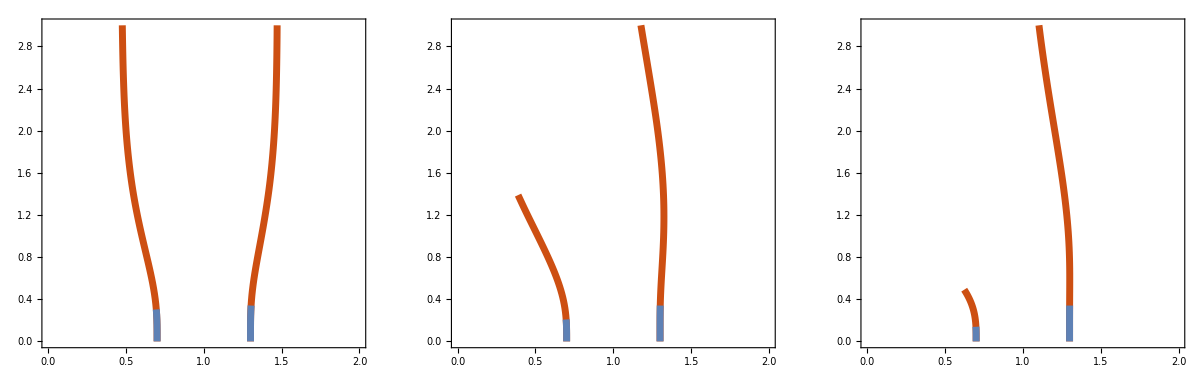

```mathematica
cutTable={105,105,105};
range={1,10,15};
GraphicsRow[
Table[compare1growth[datas,{range[[i]]},cutTable[[i]]],{i,1,3}],
ImageSize->1200]
```

## Neumann BC and comparison with FreeFEM

```mathematica
datas=OpenJSONData[];(*data from laplace_neumann*)
```

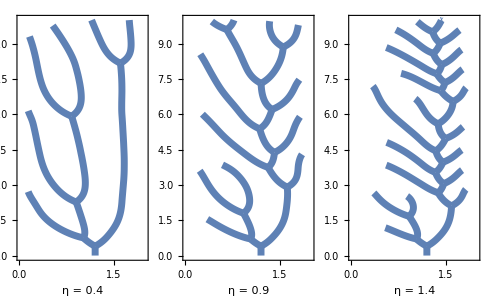

```mathematica
compareRow[datas,{5,10,15}]
```

{laplace_neumann/freefem/original_lap5.msh,laplace_neumann/freefem/original_lap10.msh,laplace_neumann/freefem/original_lap15.msh}

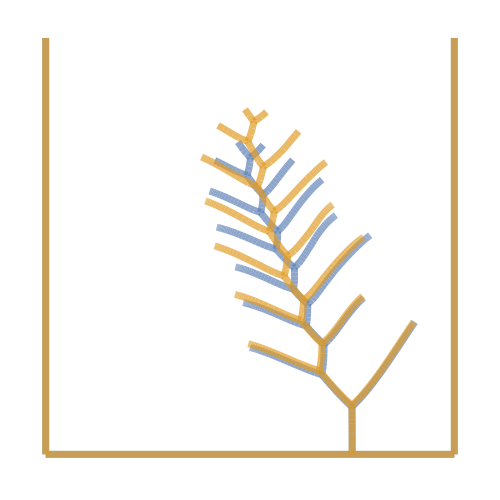

```mathematica
SetDirectory[NotebookDirectory[]];
filesNames=Table["laplace_neumann/freefem/original_lap"<>ToString[n]<>".msh",{n,{5,10,15}}]
compare1msh[{"laplace_neumann/freefem/original_lap15.msh","laplace_neumann/freefem/lap15.msh"},{1,2}]
```

### FreeFem functions

```mathematica
compare1msh[data_, range_]:=Module[{savedOpt=Options[Graphics],image,lbl=Style["η = "<>ToString[Row[(range-1)/10.,", "]],Black, 16]},
image=Graphics[Flatten[{Opacity[0.7],Thickness[0.01],Table[{ColorData[97, "ColorList"][[i]],takeNetwork[data[[range[[i]]]]]},{i,range//Length}]}],
PlotRange->{{-1,1},{0,3}},AspectRatio->1,ImageSize->500(*,
Frame->{{True,True},{True,False}},FrameLabel->{{None,None},{lbl,None}},FrameTicksStyle->Directive[Black,16]*)];
Legended[image,Grid[Table[{ColorData[97, "ColorList"][[i]],data[[range[[i]]]]},{i,range//Length}]]]]
```

```mathematica
takeNetwork[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]+data[[1]][[2]]);;(1+data[[1]][[1]]+data[[1]][[2]]+data[[1]][[3]])]]][[1;;2]]];
getLineCoordinates[x_]:=Module[{},Line[{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]]}]];
Map[getLineCoordinates,connections]
]

takeMesh[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]];
getLineCoordinates[x_]:=Module[{},Line[{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]],data[[1+x[[3]]]][[1;;2]],data[[1+x[[1]]]][[1;;2]]}]];
Map[getLineCoordinates,connections]
]

takeTriangles[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]];
getLineCoordinates[x_]:=Module[{},Triangle[{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]],data[[1+x[[3]]]][[1;;2]]}]];
Map[getLineCoordinates,connections]
]

takePoints[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]]
]

takeCoords[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]];
getLineCoordinates[x_]:=Module[{},{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]],data[[1+x[[3]]]][[1;;2]],data[[1+x[[1]]]][[1;;2]]}];
Map[getLineCoordinates,connections]
]

takeAngles[file_]:=Module[{},
connections=takeCoords[file];

Angle[x_]:=Module[{},{N[VectorAngle[x[[1]]-x[[2]],x[[3]]-x[[2]]]/Degree],
N[VectorAngle[x[[2]]-x[[3]],x[[4]]-x[[3]]]/Degree],
N[VectorAngle[x[[3]]-x[[1]],x[[2]]-x[[1]]]/Degree]}];
Map[Angle,connections]
]
```

## Comparison with analytical results

Comparison of the simulated and analytical solutions for tip velocity in the channel of width 2 and infinite length (150 in numerical solution).

Source: T.Gubiec and P.Szymczak, Fingered growth in channel geometry : A Loewner - equation approach, Phys.Rev.E 77, 041602 (2008).

#### Analytical value of velocity

```mathematica
v[H_, η_]:=(Pi/2*Coth[Pi/2*H])^(-η/2)
```

```mathematica
NSolve[v[H,1]==0.7,H]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{H→0.649077},{H→0.649077}}

## Sandbox in sandbox

```mathematica
datas=OpenJSONData[];
```

```mathematica
compareRow[datas,{5,10,15}]
```

-Graphics-